```mathematica
Needs["Splines`"]
```

# Типовой расчет

Глёза Егор, группа 221701, вариант 1

## Условие

Функция  задана в виде таблицы — известны значения  в 25 равноотстоящих точках  (узлах сетки с постоянным шагом ) на отрезке .
Требуется средствами пакета Mathematica аппроксимировать функцию на заданном отрезке:
	- выбрать и применить соответствующую встроенную функцию пакета;
	- записать уравнение полученной аппроксимирующей функции;
	- вывести график аппроксимирующей функции на отрезке  и значения исходной функции в узлах.

```mathematica
tab=
{
{0.3,-1.10525},
{0.348,-1.07996},
{0.396,-1.1225},
{0.444,-1.05986},
{0.492,-1.06783},
{0.54,-0.978257},
{0.588,-0.955869},
{0.636,-0.846209},
{0.684,-0.794931},
{0.732,-0.671395},
{0.78,-0.593028},
{0.828,-0.459459},
{0.876,-0.354877},
{0.924,-0.214726},
{0.972,-0.0844691},
{1.02,0.0593841},
{1.068,0.215},
{1.116,0.360097},
{1.164,0.540909},
{1.212,0.685119},
{1.26,0.891074},
{1.308,1.03252},
{1.356,1.26364},
{1.404,1.40065},
{1.452,1.65703}
};
a=tab[[1,1]];
b=tab[[-1,1]];
n=Length[tab];
h=(b-a)/(n-1);
```

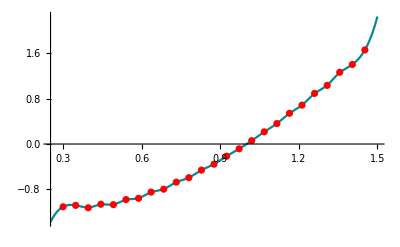

```mathematica
g =Interpolation[tab, x]//Simplify;
p=ListPlot[tab, PlotStyle->{Red}];
gr=Plot[g, {x,a-h,b+h}];
Show[gr, p]
```

## Задание 1

Постройте для функции  интерполяционный многочлен степени  и многочлены меньшей степени на отрезке, используя не все узлы сетки.

-3.72586×10^10+1.25125×10^12 x-1.99039×10^13 x^2+1.99635×10^14 x^3-1.41776×10^15 x^4+7.58903×10^15 x^5-3.18227×10^16 x^6+1.07247×10^17 x^7-2.95698×10^17 x^8+6.75393×10^17 x^9-1.28916×10^18 x^10+2.06833×10^18 x^11-2.79881×10^18 x^12+3.19823×10^18 x^13-3.08365×10^18 x^14+2.50118×10^18 x^15-1.69747×10^18 x^16+9.5593×10^17 x^17-4.41327×10^17 x^18+1.64161×10^17 x^19-4.79738×10^16 x^20+1.06021×10^16 x^21-1.66518×10^15 x^22+1.65589×10^14 x^23-7.8352×10^12 x^24

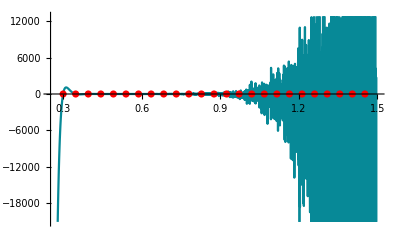

```mathematica
g=InterpolatingPolynomial[tab,x]//Simplify
gr25=Plot[g,{x,a-h,b+h}];
Show[gr25,p]
```

##### При использовании значений функции в нечётных узлах:

24.5246-422.856 x+3136.48 x^2-13805.4 x^3+40088.3 x^4-80900.5 x^5+116489. x^6-120751. x^7+89546.3 x^8-46385.3 x^9+15948.6 x^10-3271.19 x^11+302.956 x^12

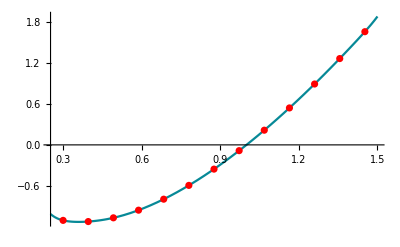

```mathematica
g12=InterpolatingPolynomial[tab[[;;;;2]],x]//Simplify
gr12=Plot[g12,{x,a-h,b+h}];
p12=ListPlot[tab[[;;;;2]], PlotStyle->{Red}];
Show[gr12,p12]
```

##### При использовании значений функции в каждом третьем узле:

-38.3134+426.282 x-2023.8 x^2+5226.1 x^3-8071.29 x^4+7678.81 x^5-4411.97 x^6+1404.28 x^7-190.107 x^8

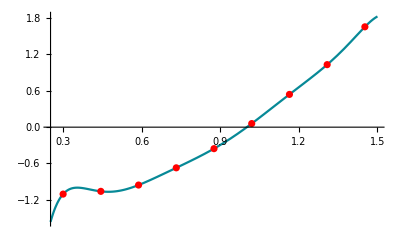

```mathematica
g8=InterpolatingPolynomial[tab[[;;;;3]],x]//Simplify
gr8=Plot[g8,{x,a-h,b+h}];
p8=ListPlot[tab[[;;;;3]], PlotStyle->{Red}];
Show[gr8,p8]
```

##### При использовании значений функции в каждом пятом узле:

-1.07125-0.0981152 x-0.936984 x^2+3.319 x^3-1.21634 x^4

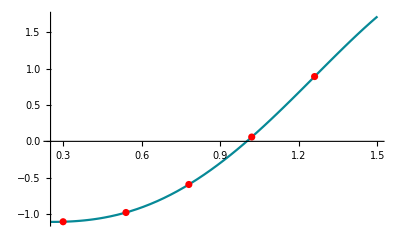

```mathematica
g5=InterpolatingPolynomial[tab[[;;;;5]],x]//Simplify
gr5=Plot[g5,{x,a-h,b+h}];
p5=ListPlot[tab[[;;;;5]], PlotStyle->{Red}];
Show[gr5,p5]
```

## Задание 2

Постройте сплайны, аппроксимирующие функцию  по значениям в узлах, выведите графики и сравните с графиками интерполяционных многочленов степени , построенных по тем же узлам.

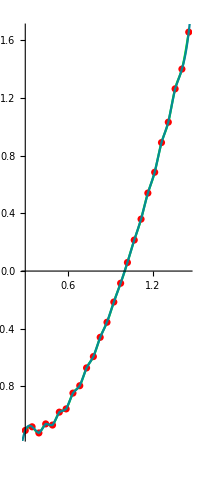

```mathematica
s=SplineFit[tab, Cubic];
Show[ParametricPlot[s[t],{t,0,25}, PlotStyle->{Green}],p,gr]
```

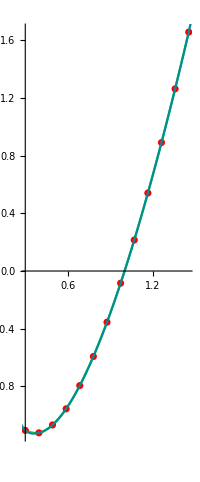

```mathematica
s12=SplineFit[tab[[;;;;2]], Cubic];
Show[ParametricPlot[s12[t],{t,0,12}, PlotStyle->{Green}],p12,gr12]
```

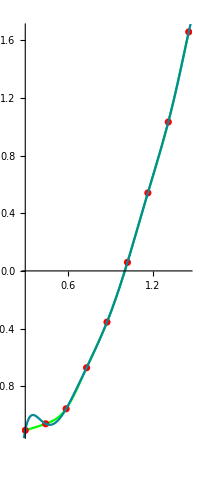

```mathematica
s8=SplineFit[tab[[;;;;3]], Cubic];
Show[ParametricPlot[s8[t],{t,0,8}, PlotStyle->{Green}],p8,gr8]
```

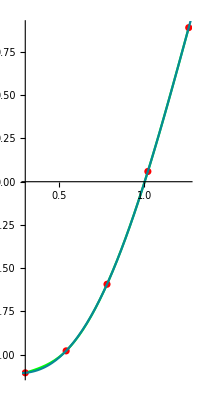

```mathematica
s5=SplineFit[tab[[;;;;5]], Cubic];
Show[ParametricPlot[s5[t],{t,0,5}, PlotStyle->{Green}],p5,gr5]
```

## Задание 3

Постройте для функции  многочлены наилучшего среднеквадратичного приближения  степени . Вычислите для каждого многочлена сумму квадратов отклонения в узлах, сравните их значения и сделайте выводы. Выведите графики узлов и многочленов , аппроксимирующих
функцию.

```mathematica
X[x_,n_]:=Table[x^i,{i,0,n}];
```

```mathematica
f1=Fit[tab, {1,x}, x]
```

-2.27848+2.45109 x

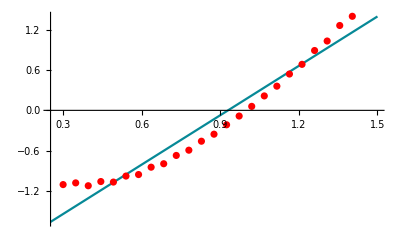

```mathematica
Show[Plot[f1,{x,a-h,b+h}],p]
```

##### Сумма квадратов отклонения

```mathematica
Sum[(tab[[i,2]]-f1/.x->tab[[i,1]])^2,{i, 1, Length[tab]}]
```

1.00288

```mathematica
f2=Fit[tab, {1,x,x^2}, x]
```

-1.07764-0.797805 x+1.85439 x^2

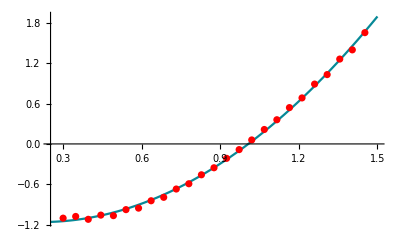

```mathematica
Show[Plot[f2,{x,a-h,b+h}],p]
```

##### Сумма квадратов отклонения

```mathematica
Sum[(tab[[i,2]]-f2/.x->tab[[i,1]])^2,{i, 1, Length[tab]}]
```

0.0204319

## Задание 4

Вычислите определенный интеграл  следующими методами:
	- методами левых, правых и средних прямоугольников;
	- методом трапеций;
	- методом парабол (Симпсона).
Сравните полученные приближенные значения интеграла и сделайте выводы о точности результата

##### Метод левых прямоугольников

```mathematica
h Total[tab[[1;;-2,2]]]
```

-0.237131

##### Метод левых прямоугольников

```mathematica
h Total[tab[[2;;-1,2]]]
```

-0.104541

##### Метод средних прямоугольников

```mathematica
2h Total[tab[[2;;;;2,2]]]
```

-0.170121

##### Метод трапеций

```mathematica
h (Total[tab[[2;;-2,2]]]+Total[tab[[{1,-1},2]]]/2)
```

-0.170836

##### Метод парабол

```mathematica
h/3 (2Total[tab[[2;;-2;;2,2]]]+4Total[tab[[3;;-2;;2,2]]]+Total[tab[[{1,-1},2]]])
```

-0.179903

## Задание 5

Постройте с помощью формул численного дифференцирования первого и второго порядка точности таблицу первых и вторых производных функции  в 25 узлах сетки. Сравните полученные результаты и сделайте выводы

### Первая производная

##### Первая степень точности

```mathematica
Differences[tab[[;;,2]]~Join~{f2/.x->tab[[-1,1]]+h}]/h//TableForm
```

0.526875
-0.88625
1.305
-0.166042
1.8661
0.466417
2.28458
1.06829
2.57367
1.63265
2.78269
2.17879
2.91981
2.71369
2.99694
3.242
3.02285
3.76692
3.00438
4.29073
2.94679
4.815
2.85437
5.34125
5.02094

##### Вторая степень точности

```mathematica
Table[(tab[[i+1,2]]-tab[[i-1,2]])/(2h),{i,2,n-1}]~Join~{((f2/.x->tab[[-1,1]]+h)-tab[[-2,2]])/(2h)}//TableForm
```

-0.179687
0.209375
0.569479
0.850031
1.16626
1.3755
1.67644
1.82098
2.10316
2.20767
2.48074
2.5493
2.81675
2.85531
3.11947
3.13243
3.39489
3.38565
3.64755
3.61876
3.8809
3.83469
4.09781
5.1811

### Вторая производная

##### Вторая степень точности

```mathematica
Differences[tab[[;;,2]]~Join~{f2/.x->tab[[-1,1]]+h}]/h^2//TableForm
```

10.9766
-18.4635
27.1875
-3.4592
38.8772
9.71701
47.5955
22.2561
53.6181
34.0135
57.9727
45.3915
60.8294
56.5351
62.4363
67.5416
62.9761
78.4774
62.5911
89.3902
61.3915
100.313
59.4661
111.276
104.603